```mathematica
A1=IdentityMatrix[5]-0.5*Table[Table[1,{i,1,5}],{j,1,5}];
A2 = RandomVariate[GaussianOrthogonalMatrixDistribution[5]];
InHQ[X_]:=Tr[X]≥0&&Tr[X]^2-Tr[X.X] ≥0&&Tr[X]^3-3*Tr[X]*Tr[X.X]+2*Tr[X.X.X]≥0
Show[RegionPlot[InHQ[x * A1 + y *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2},BoundaryStyle->None, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False],RegionPlot[PositiveSemidefiniteMatrixQ[x * A1 + y *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,BoundaryStyle->None,Frame->False]]
```

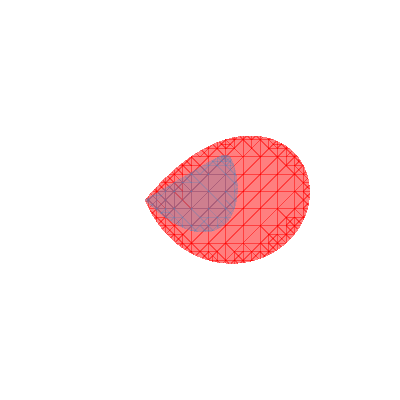

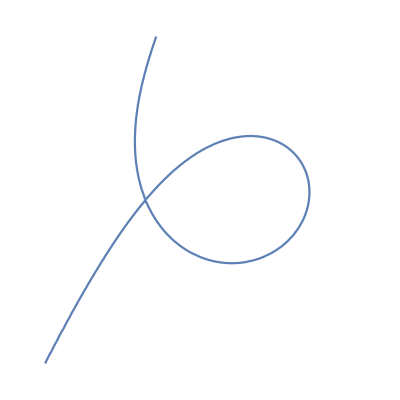

```mathematica
ContourPlot[Evaluate[Tr[X]^3-3*Tr[X]*Tr[X.X]+2*Tr[X.X.X]/.{X->x * A1 + y *A2 + IdentityMatrix[5]}]==0, {x,-3,3},{y,-2,2},Axes->False,BoundaryStyle->None,Frame->False]
```

```mathematica
Tr[X]^2-Tr[X.X]/.{X->DiagonalMatrix[{x,y,z,w,u}]}
```

-u^2-w^2-x^2-y^2-z^2+(u+w+x+y+z)^2

```mathematica
Expand[-u^2-w^2-x^2-y^2-z^2+(u+w+x+y+z)^2]
```

2 u w+2 u x+2 w x+2 u y+2 w y+2 x y+2 u z+2 w z+2 x z+2 y z

```mathematica
Expand[(u+w+x+y+z)^3-3 (u+w+x+y+z) (u^2+w^2+x^2+y^2+z^2)+2 (u^3+w^3+x^3+y^3+z^3)]
```

6 u w x+6 u w y+6 u x y+6 w x y+6 u w z+6 u x z+6 w x z+6 u y z+6 w y z+6 x y z

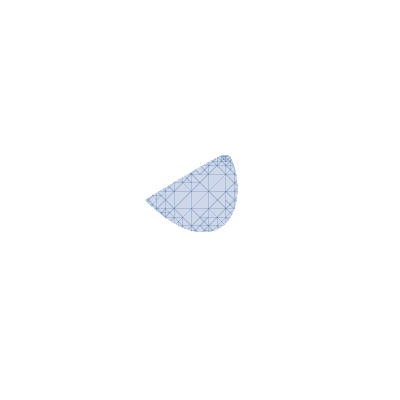

```mathematica
Show[RegionPlot[PositiveSemidefiniteMatrixQ[x * A1 + y *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2},Axes->False,BoundaryStyle->None,Frame->False]]
```

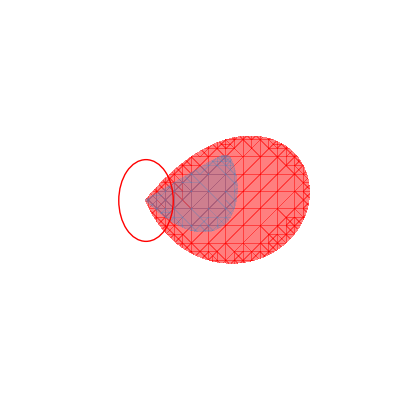

```mathematica
Show[RegionPlot[InHQ[x * A1 + y *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None],RegionPlot[PositiveSemidefiniteMatrixQ[x * A1 + y *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,Frame->False,BoundaryStyle->None],Graphics[{Red, Circle[{-1,0},0.5]}]]
```

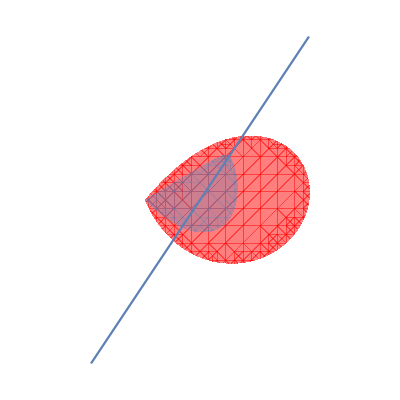

```mathematica
Show[RegionPlot[InHQ[x * A1 + y *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None],RegionPlot[PositiveSemidefiniteMatrixQ[x * A1 + y *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,Frame->False,BoundaryStyle->None],ContourPlot[x==y,{x,-3,3},{y,-2,2}]]
```

```mathematica
Show[RegionPlot[InHQ[(x-y)* A1 + (x+y) *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None],RegionPlot[PositiveSemidefiniteMatrixQ[(x+-y) * A1 + (x+y) *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,Frame->False,BoundaryStyle->None],ContourPlot[y==0,{x,-3,3},{y,-2,2}]]
```

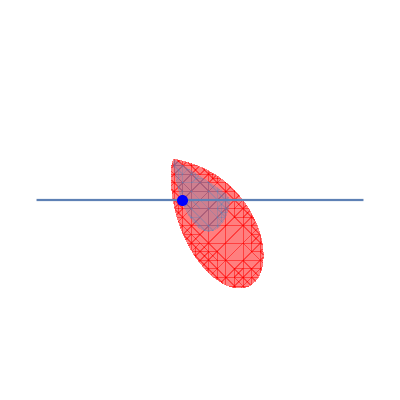

```mathematica
Show[RegionPlot[InHQ[(x-y)* A1 + (x+y) *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None],RegionPlot[PositiveSemidefiniteMatrixQ[(x+-y) * A1 + (x+y) *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,Frame->False,BoundaryStyle->None],ContourPlot[y==0,{x,-3,3},{y,-2,2}],Graphics[{PointSize[0.02],Blue,Point[{-0.3300669210231116,0}]}]]
```

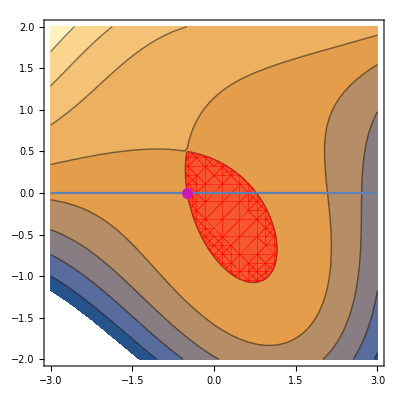

```mathematica
Show[ContourPlot[Evaluate[(Tr[X]^3-3*Tr[X]*Tr[X.X]+2*Tr[X.X.X])/150/.X->(x-y)* A1 + (x+y) *A2 +IdentityMatrix[5]],{x,-3,3},{y,-2,2}],RegionPlot[InHQ[(x-y)* A1 + (x+y) *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None],ContourPlot[y==0,{x,-3,3},{y,-2,2}],Graphics[{PointSize[0.02],CMYKColor[0.2,0.9,0.3],Point[{-0.5,0}]}]]
```

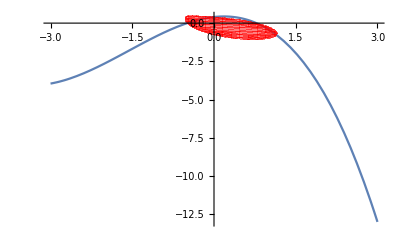

```mathematica
Show[Plot[Evaluate[(Tr[X]^3-3*Tr[X]*Tr[X.X]+2*Tr[X.X.X])/150/.X->x* A1 +x*A2 +IdentityMatrix[5]],{x,-3,3}],RegionPlot[InHQ[(x-y)* A1 + (x+y) *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False,BoundaryStyle->None]]
```

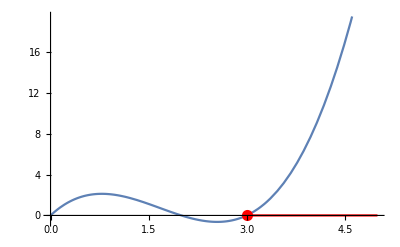

```mathematica
Show[Plot[(x-0)*(x-3)*(x-2), {x, 0,5},Ticks->False],Plot[0, {x,3,5}, PlotStyle->Red,Ticks->False],Graphics[{PointSize[0.02],Red,Point[{3,0}]}]]
```

```mathematica
Eigenvalues[A1+A2]
```

{3.33148,2.14244,-1.72792,1.51769,-1.24547}

```mathematica
Solve[Evaluate[Tr[X]^3-3*Tr[X]*Tr[X.X]+2*Tr[X.X.X]==0/.{X->x*A1+x*A2+IdentityMatrix[5]}],x]
```

{{x→-1.14702},{x→-0.404859},{x→1.07425}}

{{x→-0.484272},{x→-0.330067},{x→0.533653},{x→0.718016},{x→4.10387}}

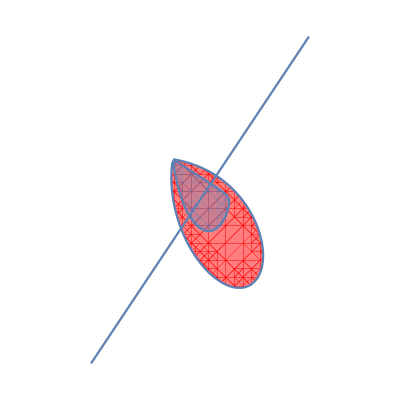
Rotate[-Graphics-,Null,-0.981748]

```mathematica
Solve[Evaluate[Det[X]==0/.{X->x*A1+x*A2+IdentityMatrix[5]}],x]
Rotate[Show[RegionPlot[InHQ[(x-y)* A1 + (x+y) *A2 + IdentityMatrix[5]],{x,-3,3},{y,-2,2}, PlotStyle->{Red,Opacity[0.5]},Axes->False,Frame->False],RegionPlot[PositiveSemidefiniteMatrixQ[(x-y) * A1 + (x+y) *A2 + IdentityMatrix[5]], {x,-3,3},{y,-2,2},Axes->False,Frame->False],ContourPlot[x==y,{x,-3,3},{y,-2,2}]],,-Pi/3.2]
```

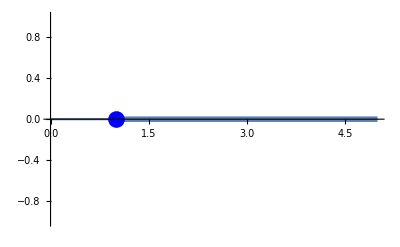

```mathematica
Show[Plot[0,{y,0,5}, Ticks->False],Plot[0,{y,1,5}, PlotStyle->Thickness[0.01], Ticks->False],Graphics[{PointSize[0.03], Blue,Point[{1,0}]}]]
```

```mathematica
N[Table[Cos[i*Pi / 5], {i, 0,5}]]
```

{1.,0.809017,0.309017,-0.309017,-0.809017,-1.}

```mathematica
V={{1,1,1,1,1},{x1,x2,x3,x4,x5},{x1,x2,x3,x4,x5}^2,{x1,x2,x3,x4,x5}^3}
```

{{1,1,1,1,1},{x1,x2,x3,x4,x5},{x1^2,x2^2,x3^2,x4^2,x5^2},{x1^3,x2^3,x3^3,x4^3,x5^3}}

```mathematica
X=Simplify[Transpose[V].Inverse[V.Transpose[V]].{1,y,y^2,y^3}]
```

{(x3 (x3-x4)^2 x4 (x3-x5)^2 (x4-x5)^2 x5 (x3-y) (x4-y) (x5-y)+10+x1^2 1-x1^3 (1))/(2 (1)),1/(2 (1)),1/(2 1),(-2 8 y+16)/(2 (1)),1/(2 (1))}
 |  |  |  |

```mathematica
SymmetricPolynomial[3, {(y-x2)/(x1-x2), (y-x3)/(x1-x3),(y-x3)/(x1-x3),(y-x4)/(x1-x4)}]
```

((-x2+y) (-x3+y)^2)/((x1-x2) (x1-x3)^2)+(2 (-x2+y) (-x3+y) (-x4+y))/((x1-x2) (x1-x3) (x1-x4))+((-x3+y)^2 (-x4+y))/((x1-x3)^2 (x1-x4))

```mathematica
Simplify[((-x2+y) (-x3+y)^2)/((x1-x2) (x1-x3)^2)+(2 (-x2+y) (-x3+y) (-x4+y))/((x1-x2) (x1-x3) (x1-x4))+((-x3+y)^2 (-x4+y))/((x1-x3)^2 (x1-x4))]
```

((x3-y) (y (-3 x3 x4+2 x3 y+x4 y)+x2 (4 x3 x4-3 x3 y-2 x4 y+y^2)-x1 (x3 x4+x2 (x3+2 x4-3 y)-2 x3 y-3 x4 y+4 y^2)))/((x1-x2) (x1-x3)^2 (x1-x4))

```mathematica
Simplify[X[[1]]]
```

(x3 (x3-x4)^2 x4 (x3-x5)^2 (x4-x5)^2 x5 (x3-y) (x4-y) (x5-y)+x2^6 (x4 (x4-x5)^2 x5 (x4-y) (x5-y)+x3^4 (x4^2+x5 (x5-y)-x4 y)+x3 y (-x4^4+x4^3 y+x5^3 (-x5+y))+x3^2 (x4^4+x4^3 y-2 x4^2 y^2+x5^2 (x5^2+x5 y-2 y^2))+x3^3 (-2 x4^3+x4^2 y+x4 y^2+x5 (-2 x5^2+x5 y+y^2)))-x2 y (x4^3 (x4-x5)^2 x5^3 (x4-y) (x5-y)+x3^6 (x4^4+x5^3 (x5-y)-x4^3 y)+x3^3 y (-x4^6+x4^5 y+x5^5 (-x5+y))+x3^4 (x4^6+x4^5 y-2 x4^4 y^2+x5^4 (x5^2+x5 y-2 y^2))+x3^5 (-2 x4^5+x4^4 y+x4^3 y^2+x5^3 (-2 x5^2+x5 y+y^2)))+x2^3 (x3 y^2 (x4^6+x5^5 (x5-y)-x4^5 y)+2 x3^4 (x4^5+x4^4 y-x4^3 y^2-x4^2 y^3+x5^2 (x5-y) (x5+y)^2)-x4 (x4-x5)^2 x5 (x4-y) (x5-y) (x5^2 y+x4^2 (2 x5+y)+2 x4 x5 (x5+2 y))+x3^2 y (x4^6+x4^5 y-2 x4^4 y^2+x5^4 (x5^2+x5 y-2 y^2))+x3^6 (-2 x4^3+x4^2 y+x4 y^2+x5 (-2 x5^2+x5 y+y^2))-2 x3^3 (x4^6+x4^5 y+x4^4 y^2-3 x4^3 y^3+x5^3 (x5^3+x5^2 y+x5 y^2-3 y^3))+x3^5 (2 x4^4-2 x4^3 y+x4^2 y^2-x4 y^3+x5 (2 x5^3-2 x5^2 y+x5 y^2-y^3)))-x2^5 (x4 (x4-x5)^2 x5 (x4-y) (x5-y) (2 x4+2 x5+y)+2 x3^5 (x4^2+x5 (x5-y)-x4 y)+x3^4 (-2 x4^3+x4^2 y+x4 y^2+x5 (-2 x5^2+x5 y+y^2))+x3 y (-2 x4^5+x4^4 y+x4^3 y^2+x5^3 (-2 x5^2+x5 y+y^2))+x3^2 (2 x4^5+x4^4 y-x4^3 y^2-2 x4^2 y^3+x5^2 (2 x5^3+x5^2 y-x5 y^2-2 y^3))+x3^3 (-2 x4^4+2 x4^3 y-x4^2 y^2+x4 y^3+x5 (-2 x5^3+2 x5^2 y-x5 y^2+y^3)))+x2^4 (x3^6 (x4^2+x5 (x5-y)-x4 y)+2 x3^3 (x4^5+x4^4 y-x4^3 y^2-x4^2 y^3+x5^2 (x5-y) (x5+y)^2)+x4 (x4-x5)^2 x5 (x4-y) (x5-y) (x4^2+2 x4 (2 x5+y)+x5 (x5+2 y))-x3 y (x4^6+x4^5 y-2 x4^4 y^2+x5^4 (x5^2+x5 y-2 y^2))+x3^5 (2 x4^3-x4^2 y-x4 y^2+x5 (2 x5^2-x5 y-y^2))+x3^2 (x4^6-x4^5 y+2 x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3))+2 x3^4 (-3 x4^4+x4^3 y+x4^2 y^2+x4 y^3+x5 (-3 x5^3+x5^2 y+x5 y^2+y^3)))+x2^2 (-2 x3^2 y^2 (x4^6+x5^5 (x5-y)-x4^5 y)+x4^2 (x4-x5)^2 x5^2 (x4-y) (x5-y) (2 x5 y+x4 (x5+2 y))+x3^6 (x4^4+x4^3 y-2 x4^2 y^2+x5^2 (x5^2+x5 y-2 y^2))+x3^3 y (x4^6+x4^5 y-2 x4^4 y^2+x5^4 (x5^2+x5 y-2 y^2))+x3^4 (x4^6-x4^5 y+2 x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3))+x3^5 (-2 x4^5-x4^4 y+x4^3 y^2+2 x4^2 y^3+x5^2 (-2 x5^3-x5^2 y+x5 y^2+2 y^3)))-x1 (-2 x4^3 (x4-x5)^2 x5^3 (x4-y) (x5-y) y-x3^2 x4 (x4-x5)^2 x5 (x4-y) (x5-y) (x4 x5^2+x4^2 (x5-y)-x5^2 y)+x3 x4^2 (x4-x5)^2 x5^2 (x4-y) (x5-y) (x5 y+x4 (x5+y))+x3^6 (x4^4 (x5-2 y)-x4^2 x5 (x5-y)^2+2 x5^3 y (-x5+y)-x4^3 (x5^2-2 y^2)+x4 (x5^4-x5^2 y^2))+x2^6 (x4^4 (x5-2 y)+x3^4 (x4+x5-2 y)-x4^2 x5 (x5-y)^2+2 x5^3 y (-x5+y)-x4^3 (x5^2-2 y^2)-x3^3 (x4^2+x5^2-2 y^2)-x3^2 (x4^3+x5 (x5-y)^2-2 x4^2 y+x4 y^2)+x4 (x5^4-x5^2 y^2)+x3 (x4^4+x5^4-x4^2 y^2-x5^2 y^2))+x3^5 (-2 x4^5 (x5-2 y)+x4^4 (x5^2-2 y^2)+2 x5^3 y (2 x5^2-x5 y-y^2)+x4^3 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3)+x4^2 x5 (x5^3-2 x5^2 y+y^3)+x4 x5^2 (-2 x5^3+x5 y^2+y^3))+x3^3 (x4 x5^4 (x5-y) y^2+2 x5^5 (x5-y) y^2-x4^6 (x5^2-2 y^2)+x4^5 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3)+x4^4 x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3)+2 x4^3 x5^2 (x5^3+x5^2 y-3 x5 y^2+y^3)+x4^2 x5^3 (-x5^3-2 x5^2 y+x5 y^2+2 y^3))+x3^4 (x4^6 (x5-2 y)+x4^5 (x5^2-2 y^2)-2 x5^4 y (x5^2+x5 y-2 y^2)-2 x4^4 (x5^3-2 y^3)+x4^2 x5^2 (x5^3+x5 y^2-2 y^3)+x4^3 x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3)+x4 (x5^6-x5^3 y^3))+x2^2 (-x4 (x4-x5)^2 x5 (x4-y) (x5-y) (x4 x5^2+x4^2 (x5-y)-x5^2 y)-x3^6 (x4^3+x5 (x5-y)^2-2 x4^2 y+x4 y^2)+2 x3^2 y (x4^6+x5^6-x4^4 y^2-x5^4 y^2)+x3^5 (x4^4+x5^4-2 x4^3 y-2 x5^3 y+x4 y^3+x5 y^3)+x3 y^2 (-x4^6+x4^5 y+x5^5 (-x5+y))-x3^3 (x4^6+2 x4^5 y-x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3+2 x5^2 y-x5 y^2-2 y^3))+x3^4 (x4^5+x4^3 y^2-2 x4^2 y^3+x5^2 (x5^3+x5 y^2-2 y^3)))+x2^4 (x4^6 (x5-2 y)+x3^6 (x4+x5-2 y)+x4^5 (x5^2-2 y^2)+x3^5 (x4^2+x5^2-2 y^2)-2 x5^4 y (x5^2+x5 y-2 y^2)-2 x4^4 (x5^3-2 y^3)-2 x3^4 (x4^3+x5^3-2 y^3)+x4^2 x5^2 (x5^3+x5 y^2-2 y^3)+x4^3 x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3)+x4 (x5^6-x5^3 y^3)+x3 (x4^6+x5^6-x4^3 y^3-x5^3 y^3)+x3^2 (x4^5+x4^3 y^2-2 x4^2 y^3+x5^2 (x5^3+x5 y^2-2 y^3))+x3^3 (-2 x4^4+2 x4^3 y+x4^2 y^2-x4 y^3+x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3)))+x2^3 (x4 x5^4 (x5-y) y^2+2 x5^5 (x5-y) y^2+x3 y^2 (x4^5+x5^4 (x5-y)-x4^4 y)-x4^6 (x5^2-2 y^2)-x3^6 (x4^2+x5^2-2 y^2)+x4^5 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3)+x3^5 (2 x4^3+2 x5^3-2 x4^2 y-2 x5^2 y+x4 y^2+x5 y^2-2 y^3)+x4^4 x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3)+2 x4^3 x5^2 (x5^3+x5^2 y-3 x5 y^2+y^3)+x4^2 x5^3 (-x5^3-2 x5^2 y+x5 y^2+2 y^3)-x3^2 (x4^6+2 x4^5 y-x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3+2 x5^2 y-x5 y^2-2 y^3))+x3^4 (-2 x4^4+2 x4^3 y+x4^2 y^2-x4 y^3+x5 (-2 x5^3+2 x5^2 y+x5 y^2-y^3))+2 x3^3 (x4^5+x4^4 y-3 x4^3 y^2+x4^2 y^3+x5^2 (x5^3+x5^2 y-3 x5 y^2+y^3)))+x2^5 (-2 x4^5 (x5-2 y)-2 x3^5 (x4+x5-2 y)+x4^4 (x5^2-2 y^2)+x3^4 (x4^2+x5^2-2 y^2)+2 x5^3 y (2 x5^2-x5 y-y^2)+x4^3 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3)+x3^3 (2 x4^3+2 x5^3-2 x4^2 y-2 x5^2 y+x4 y^2+x5 y^2-2 y^3)+x4^2 x5 (x5^3-2 x5^2 y+y^3)+x4 x5^2 (-2 x5^3+x5 y^2+y^3)+x3^2 (x4^4+x5^4-2 x4^3 y-2 x5^3 y+x4 y^3+x5 y^3)+x3 (-2 x4^5+x4^3 y^2+x4^2 y^3+x5^2 (-2 x5^3+x5 y^2+y^3)))+x2 (x3^3 y^2 (x4^5+x5^4 (x5-y)-x4^4 y)+x3^6 (x4^4+x5^4-x4^2 y^2-x5^2 y^2)+x3^4 (x4^6+x5^6-x4^3 y^3-x5^3 y^3)+x3^2 y^2 (-x4^6+x4^5 y+x5^5 (-x5+y))+x4^2 (x4-x5)^2 x5^2 (x4-y) (x5-y) (x5 y+x4 (x5+y))+x3^5 (-2 x4^5+x4^3 y^2+x4^2 y^3+x5^2 (-2 x5^3+x5 y^2+y^3))))+x1^2 (-2 x4^2 (x4-x5)^2 x5^2 (x4+x5) (x4-y) (x5-y) y+x3 x4 (x4-x5)^2 x5 (x4-y) (x5-y) (2 x5^2 y+x4^2 (x5+2 y)+x4 x5 (x5+3 y))+x3^6 (x4^3 (x5-2 y)+2 x5^2 y (-x5+y)+x4 x5 (x5^2+x5 y-2 y^2)+x4^2 (-2 x5^2+x5 y+2 y^2))+x3^3 (x4^6 (x5-2 y)+x4^5 x5 (x5-y)-2 x5^6 y+2 x5^4 y^3+x4 x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3)-2 x4^3 x5 (x5^3-3 x5^2 y+x5 y^2+y^3)+x4^2 x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3)+x4^4 (-2 x5^3-x5^2 y+2 x5 y^2+2 y^3))-x3^5 (x4^4 (x5-2 y)-2 x5^4 y+2 x5^2 y^3+x4^3 x5 (-x5+y)-x4^2 (x5^3-2 y^3)+x4 (x5^4+x5^3 y-2 x5 y^3))-x2^5 (x4^4 (x5-2 y)+x3^4 (x4+x5-2 y)-2 x5^4 y+2 x5^2 y^3+x4^3 x5 (-x5+y)-x3^3 (x4^2+x5 (x5-y)-x4 y)-x4^2 (x5^3-2 y^3)-x3^2 (x4^3+x5^3-2 y^3)+x4 (x5^4+x5^3 y-2 x5 y^3)+x3 (x4^4+x5^4+x4^3 y+x5^3 y-2 x4 y^3-2 x5 y^3))-x3^4 (x4^5 (x5-2 y)-2 x5^3 (x5-y)^2 y-2 x4^4 (x5^2-2 y^2)+x4^3 (2 x5^3+x5^2 y-2 x5 y^2-2 y^3)+x4 x5^2 (x5^3-2 x5 y^2+y^3)+x4^2 (-2 x5^4+x5^3 y+x5 y^3))+x3^2 (2 x5^5 (x5-y) y^2+x4 x5^4 y (x5^2-y^2)+x4^6 (-2 x5^2+x5 y+2 y^2)+x4^5 (x5^3-2 y^3)+x4^3 x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3)+x4^4 (2 x5^4-x5^3 y-x5 y^3)-2 x4^2 (x5^6-x5^3 y^3))+x2^6 (x4^3 (x5-2 y)+x3^3 (x4+x5-2 y)+2 x5^2 y (-x5+y)+x4 x5 (x5^2+x5 y-2 y^2)+x4^2 (-2 x5^2+x5 y+2 y^2)+x3^2 (-2 x4^2-2 x5^2+x4 y+x5 y+2 y^2)+x3 (x4^3+x4^2 y-2 x4 y^2+x5 (x5^2+x5 y-2 y^2)))-x2^4 (x4^5 (x5-2 y)+x3^5 (x4+x5-2 y)-2 x5^3 (x5-y)^2 y-2 x4^4 (x5^2-2 y^2)-2 x3^4 (x4^2+x5^2-2 y^2)+x4^3 (2 x5^3+x5^2 y-2 x5 y^2-2 y^3)+x3^3 (2 x4^3+2 x5^3+x4^2 y+x5^2 y-2 x4 y^2-2 x5 y^2-2 y^3)+x4 x5^2 (x5^3-2 x5 y^2+y^3)+x4^2 (-2 x5^4+x5^3 y+x5 y^3)+x3^2 (-2 x4^4-2 x5^4+x4^3 y+x5^3 y+x4 y^3+x5 y^3)+x3 (x4^5-2 x4^3 y^2+x4^2 y^3+x5^2 (x5^3-2 x5 y^2+y^3)))+x2 (-2 x3 y^2 (x4^6+x5^5 (x5-y)-x4^5 y)+x3^2 y (x4^6+x5^6-x4^4 y^2-x5^4 y^2)-x3^5 (x4^4+x5^4+x4^3 y+x5^3 y-2 x4 y^3-2 x5 y^3)+x4 (x4-x5)^2 x5 (x4-y) (x5-y) (2 x5^2 y+x4^2 (x5+2 y)+x4 x5 (x5+3 y))+x3^6 (x4^3+x4^2 y-2 x4 y^2+x5 (x5^2+x5 y-2 y^2))+x3^3 (x4^6-x4^5 y+2 x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3))-x3^4 (x4^5-2 x4^3 y^2+x4^2 y^3+x5^2 (x5^3-2 x5 y^2+y^3)))+x2^3 (x4^6 (x5-2 y)+x3^6 (x4+x5-2 y)+x4^5 x5 (x5-y)-2 x5^6 y+2 x5^4 y^3+x3^5 (x4^2+x5 (x5-y)-x4 y)-x3^4 (2 x4^3+2 x5^3+x4^2 y+x5^2 y-2 x4 y^2-2 x5 y^2-2 y^3)+x4 x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3)-2 x4^3 x5 (x5^3-3 x5^2 y+x5 y^2+y^3)+x4^2 x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3)+x4^4 (-2 x5^3-x5^2 y+2 x5 y^2+2 y^3)+x3 (x4^6-x4^5 y+2 x4^4 y^2-2 x4^3 y^3+x5^3 (x5^3-x5^2 y+2 x5 y^2-2 y^3))-2 x3^3 (x4^4-3 x4^3 y+x4^2 y^2+x4 y^3+x5 (x5^3-3 x5^2 y+x5 y^2+y^3))+x3^2 (x4^5-x4^4 y-2 x4^3 y^2+2 x4^2 y^3+x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3)))+x2^2 (2 x5^5 (x5-y) y^2+x4 x5^4 y (x5^2-y^2)+x4^6 (-2 x5^2+x5 y+2 y^2)+x3^6 (-2 x4^2-2 x5^2+x4 y+x5 y+2 y^2)+x3 y (x4^6+x5^6-x4^4 y^2-x5^4 y^2)+x4^5 (x5^3-2 y^3)+x3^5 (x4^3+x5^3-2 y^3)+x4^3 x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3)+x4^4 (2 x5^4-x5^3 y-x5 y^3)+x3^4 (2 x4^4+2 x5^4-x4^3 y-x5^3 y-x4 y^3-x5 y^3)-2 x4^2 (x5^6-x5^3 y^3)-2 x3^2 (x4^6+x5^6-x4^3 y^3-x5^3 y^3)+x3^3 (x4^5-x4^4 y-2 x4^3 y^2+2 x4^2 y^3+x5^2 (x5^3-x5^2 y-2 x5 y^2+2 y^3))))-x1^3 (-2 x4^2 (x4-x5)^2 x5^2 (x4-y) (x5-y) y+x3 x4 (x4-x5)^2 x5 (x4-y) (x5-y) (2 x5 y+x4 (x5+2 y))+x3^5 (x4^3 (x5-2 y)+2 x5^2 y (-x5+y)+x4 x5 (x5^2+x5 y-2 y^2)+x4^2 (-2 x5^2+x5 y+2 y^2))+x3^2 (2 x5^4 (x5-y) y^2+2 x4^3 x5 (x5-y) (x5+y)^2+x4 x5^3 y (x5^2+x5 y-2 y^2)+x4^5 (-2 x5^2+x5 y+2 y^2)-2 x4^2 x5^2 (x5^3+x5^2 y+x5 y^2-3 y^3)+x4^4 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3))-x3^4 (2 x4^4 (x5-2 y)+2 x5^2 y (-2 x5^2+x5 y+y^2)+x4^3 (-2 x5^2+x5 y+2 y^2)+x4 x5 (2 x5^3+x5^2 y-x5 y^2-2 y^3)+x4^2 (-2 x5^3+2 x5^2 y-x5 y^2+2 y^3))+x3^3 (x4^5 (x5-2 y)+2 x4^2 x5 (x5-y) (x5+y)^2+x4^4 (2 x5^2-x5 y-2 y^2)-2 x5^3 y (x5^2+x5 y-2 y^2)+x4 x5^2 (x5^3-x5^2 y+2 x5 y^2-2 y^3)+x4^3 (-6 x5^3+2 x5^2 y+2 x5 y^2+4 y^3))+x2^5 (x4^3 (x5-2 y)+x3^3 (x4+x5-2 y)+2 x5^2 y (-x5+y)+x4 x5 (x5^2+x5 y-2 y^2)+x4^2 (-2 x5^2+x5 y+2 y^2)+x3^2 (-2 x4^2-2 x5^2+x4 y+x5 y+2 y^2)+x3 (x4^3+x4^2 y-2 x4 y^2+x5 (x5^2+x5 y-2 y^2)))+x2^2 (2 x5^4 (x5-y) y^2+2 x4^3 x5 (x5-y) (x5+y)^2+x4 x5^3 y (x5^2+x5 y-2 y^2)+x4^5 (-2 x5^2+x5 y+2 y^2)+x3^5 (-2 x4^2-2 x5^2+x4 y+x5 y+2 y^2)-2 x4^2 x5^2 (x5^3+x5^2 y+x5 y^2-3 y^3)+x4^4 (2 x5^3-2 x5^2 y+x5 y^2-2 y^3)+x3^4 (2 x4^3+2 x5^3-2 x4^2 y-2 x5^2 y+x4 y^2+x5 y^2-2 y^3)+2 x3^3 (x4^4+x4^3 y-x4^2 y^2-x4 y^3+x5 (x5-y) (x5+y)^2)+x3 y (x4^5+x4^4 y-2 x4^3 y^2+x5^3 (x5^2+x5 y-2 y^2))-2 x3^2 (x4^5+x4^4 y+x4^3 y^2-3 x4^2 y^3+x5^2 (x5^3+x5^2 y+x5 y^2-3 y^3)))-x2^4 (2 x4^4 (x5-2 y)+2 x3^4 (x4+x5-2 y)+2 x5^2 y (-2 x5^2+x5 y+y^2)+x4^3 (-2 x5^2+x5 y+2 y^2)+x3^3 (-2 x4^2-2 x5^2+x4 y+x5 y+2 y^2)+x4 x5 (2 x5^3+x5^2 y-x5 y^2-2 y^3)-x3^2 (2 x4^3+2 x5^3-2 x4^2 y-2 x5^2 y+x4 y^2+x5 y^2-2 y^3)+x4^2 (-2 x5^3+2 x5^2 y-x5 y^2+2 y^3)+x3 (2 x4^4+x4^3 y-x4^2 y^2-2 x4 y^3+x5 (2 x5^3+x5^2 y-x5 y^2-2 y^3)))+x2^3 (x4^5 (x5-2 y)+x3^5 (x4+x5-2 y)+2 x4^2 x5 (x5-y) (x5+y)^2+x4^4 (2 x5^2-x5 y-2 y^2)+x3^4 (2 x4^2+2 x5^2-x4 y-x5 y-2 y^2)-2 x5^3 y (x5^2+x5 y-2 y^2)+x4 x5^2 (x5^3-x5^2 y+2 x5 y^2-2 y^3)+2 x3^3 (-3 x4^3-3 x5^3+x4^2 y+x5^2 y+x4 y^2+x5 y^2+2 y^3)+x4^3 (-6 x5^3+2 x5^2 y+2 x5 y^2+4 y^3)+2 x3^2 (x4^4+x4^3 y-x4^2 y^2-x4 y^3+x5 (x5-y) (x5+y)^2)+x3 (x4^5-x4^4 y+2 x4^3 y^2-2 x4^2 y^3+x5^2 (x5^3-x5^2 y+2 x5 y^2-2 y^3)))+x2 (-2 x3 y^2 (x4^5+x5^4 (x5-y)-x4^4 y)+x4 (x4-x5)^2 x5 (x4-y) (x5-y) (2 x5 y+x4 (x5+2 y))+x3^5 (x4^3+x4^2 y-2 x4 y^2+x5 (x5^2+x5 y-2 y^2))+x3^2 y (x4^5+x4^4 y-2 x4^3 y^2+x5^3 (x5^2+x5 y-2 y^2))+x3^3 (x4^5-x4^4 y+2 x4^3 y^2-2 x4^2 y^3+x5^2 (x5^3-x5^2 y+2 x5 y^2-2 y^3))+x3^4 (-2 x4^4-x4^3 y+x4^2 y^2+2 x4 y^3+x5 (-2 x5^3-x5^2 y+x5 y^2+2 y^3)))))/(2 (x3^2 (x3-x4)^2 x4^2 (x3-x5)^2 (x4-x5)^2 x5^2-x2 x3 (x3-x4)^2 x4 (x3-x5)^2 (x4-x5)^2 x5 (x4 x5+x3 (x4+x5))+x2^6 (x4^2 (x4-x5)^2 x5^2-x3 x4 (x4-x5)^2 x5 (x4+x5)+x3^4 (x4^2-x4 x5+x5^2)+x3^3 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)+x3^2 (x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4))-x2^5 (2 x4^2 (x4-x5)^2 x5^2 (x4+x5)+2 x3^5 (x4^2-x4 x5+x5^2)-x3 x4 (x4-x5)^2 x5 (2 x4^2+3 x4 x5+2 x5^2)+x3^4 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)-2 x3^3 (x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4)+x3^2 (2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5))+x2^4 (-x3 x4 (x4-x5)^2 x5 (x4+x5)^3+x3^6 (x4^2-x4 x5+x5^2)+x4^2 (x4-x5)^2 x5^2 (x4^2+4 x4 x5+x5^2)+x3^5 (2 x4^3-x4^2 x5-x4 x5^2+2 x5^3)+2 x3^4 (-3 x4^4+x4^3 x5+x4^2 x5^2+x4 x5^3-3 x5^4)+x3^3 (2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5)+x3^2 (x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6))+x2^2 (x4^4 (x4-x5)^2 x5^4+x3 x4^3 (x4-x5)^2 x5^3 (x4+x5)-x3^2 x4^2 (x4-x5)^2 x5^2 (3 x4^2+4 x4 x5+3 x5^2)+x3^3 x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)+x3^6 (x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4)-x3^5 (2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5)+x3^4 (x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6))+x2^3 (-2 x4^3 (x4-x5)^2 x5^3 (x4+x5)+x3 x4^2 (x4-x5)^2 x5^2 (x4^2+x5^2)+x3^6 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)+x3^2 x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)+2 x3^5 (x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4)+x3^4 (2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5)-x3^3 (2 x4^6+2 x4^5 x5+3 x4^4 x5^2-12 x4^3 x5^3+3 x4^2 x5^4+2 x4 x5^5+2 x5^6))+x1^6 (x4^2 (x4-x5)^2 x5^2-x3 x4 (x4-x5)^2 x5 (x4+x5)+x3^4 (x4^2-x4 x5+x5^2)+x3^3 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)+x3^2 (x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4)+x2^4 (x3^2+x4^2-x4 x5+x5^2-x3 (x4+x5))+x2^3 (-2 x3^3-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3+x3^2 (x4+x5)+x3 (x4^2+x5^2))+x2^2 (x3^4+x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4+x3^3 (x4+x5)-3 x3^2 (x4^2+x5^2)+x3 (x4^3+x5^3))+x2 (-x3^4 (x4+x5)-x4 (x4-x5)^2 x5 (x4+x5)+x3^3 (x4^2+x5^2)+x3^2 (x4^3+x5^3)-x3 (x4^4+x5^4)))-x1^5 (2 x4^2 (x4-x5)^2 x5^2 (x4+x5)+2 x3^5 (x4^2-x4 x5+x5^2)-x3 x4 (x4-x5)^2 x5 (2 x4^2+3 x4 x5+2 x5^2)+x3^4 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)-2 x3^3 (x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4)+x3^2 (2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5)+2 x2^5 (x3^2+x4^2-x4 x5+x5^2-x3 (x4+x5))+x2^4 (-2 x3^3-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3+x3^2 (x4+x5)+x3 (x4^2+x5^2))-2 x2^3 (x3^4+x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4-x3^3 (x4+x5)+x3^2 (x4^2+x5^2)-x3 (x4^3+x5^3))+x2^2 (2 x3^5+2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5+x3^4 (x4+x5)-2 x3^3 (x4^2+x5^2)-2 x3^2 (x4^3+x5^3)+x3 (x4^4+x5^4))+x2 (-2 x3^5 (x4+x5)+x3^4 (x4^2+x5^2)-x4 (x4-x5)^2 x5 (2 x4^2+3 x4 x5+2 x5^2)+2 x3^3 (x4^3+x5^3)+x3^2 (x4^4+x5^4)-2 x3 (x4^5+x5^5)))+x1^4 (-x3 x4 (x4-x5)^2 x5 (x4+x5)^3+x3^6 (x4^2-x4 x5+x5^2)+x4^2 (x4-x5)^2 x5^2 (x4^2+4 x4 x5+x5^2)+x3^5 (2 x4^3-x4^2 x5-x4 x5^2+2 x5^3)+2 x3^4 (-3 x4^4+x4^3 x5+x4^2 x5^2+x4 x5^3-3 x5^4)+x3^3 (2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5)+x3^2 (x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6)+x2^6 (x3^2+x4^2-x4 x5+x5^2-x3 (x4+x5))+x2^5 (2 x3^3+2 x4^3-x4^2 x5-x4 x5^2+2 x5^3-x3^2 (x4+x5)-x3 (x4^2+x5^2))+2 x2^4 (-3 x3^4-3 x4^4+x4^3 x5+x4^2 x5^2+x4 x5^3-3 x5^4+x3^3 (x4+x5)+x3^2 (x4^2+x5^2)+x3 (x4^3+x5^3))+x2^3 (2 x3^5+2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5+2 x3^4 (x4+x5)-3 x3^3 (x4^2+x5^2)-3 x3^2 (x4^3+x5^3)+2 x3 (x4^4+x5^4))+x2^2 (x3^6+x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6-x3^5 (x4+x5)+2 x3^4 (x4^2+x5^2)-3 x3^3 (x4^3+x5^3)+2 x3^2 (x4^4+x5^4)-x3 (x4^5+x5^5))-x2 (x3^6 (x4+x5)+x4 (x4-x5)^2 x5 (x4+x5)^3+x3^5 (x4^2+x5^2)-2 x3^4 (x4^3+x5^3)-2 x3^3 (x4^4+x5^4)+x3^2 (x4^5+x5^5)+x3 (x4^6+x5^6)))+x1^3 (-2 x4^3 (x4-x5)^2 x5^3 (x4+x5)+x3 x4^2 (x4-x5)^2 x5^2 (x4^2+x5^2)+x3^6 (-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3)+x3^2 x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)+2 x3^5 (x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4)+x3^4 (2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5)-x3^3 (2 x4^6+2 x4^5 x5+3 x4^4 x5^2-12 x4^3 x5^3+3 x4^2 x5^4+2 x4 x5^5+2 x5^6)+x2^6 (-2 x3^3-2 x4^3+x4^2 x5+x4 x5^2-2 x5^3+x3^2 (x4+x5)+x3 (x4^2+x5^2))+2 x2^5 (x3^4+x4^4-x4^3 x5+x4^2 x5^2-x4 x5^3+x5^4-x3^3 (x4+x5)+x3^2 (x4^2+x5^2)-x3 (x4^3+x5^3))+x2^4 (2 x3^5+2 x4^5+2 x4^4 x5-3 x4^3 x5^2-3 x4^2 x5^3+2 x4 x5^4+2 x5^5+2 x3^4 (x4+x5)-3 x3^3 (x4^2+x5^2)-3 x3^2 (x4^3+x5^3)+2 x3 (x4^4+x5^4))-x2^3 (2 x3^6+2 x4^6+2 x4^5 x5+3 x4^4 x5^2-12 x4^3 x5^3+3 x4^2 x5^4+2 x4 x5^5+2 x5^6+2 x3^5 (x4+x5)+3 x3^4 (x4^2+x5^2)-12 x3^3 (x4^3+x5^3)+3 x3^2 (x4^4+x5^4)+2 x3 (x4^5+x5^5))+x2^2 (x3^6 (x4+x5)+2 x3^5 (x4^2+x5^2)-3 x3^4 (x4^3+x5^3)+x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)-3 x3^3 (x4^4+x5^4)+2 x3^2 (x4^5+x5^5)+x3 (x4^6+x5^6))+x2 (x3^6 (x4^2+x5^2)+x4^2 (x4-x5)^2 x5^2 (x4^2+x5^2)-2 x3^5 (x4^3+x5^3)+2 x3^4 (x4^4+x5^4)-2 x3^3 (x4^5+x5^5)+x3^2 (x4^6+x5^6)))+x1^2 (x4^4 (x4-x5)^2 x5^4+x3 x4^3 (x4-x5)^2 x5^3 (x4+x5)-x3^2 x4^2 (x4-x5)^2 x5^2 (3 x4^2+4 x4 x5+3 x5^2)+x3^3 x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)+x3^6 (x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4)-x3^5 (2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5)+x3^4 (x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6)+x2^6 (x3^4+x4^4+x4^3 x5-3 x4^2 x5^2+x4 x5^3+x5^4+x3^3 (x4+x5)-3 x3^2 (x4^2+x5^2)+x3 (x4^3+x5^3))-x2^5 (2 x3^5+2 x4^5+x4^4 x5-2 x4^3 x5^2-2 x4^2 x5^3+x4 x5^4+2 x5^5+x3^4 (x4+x5)-2 x3^3 (x4^2+x5^2)-2 x3^2 (x4^3+x5^3)+x3 (x4^4+x5^4))+x2^4 (x3^6+x4^6-x4^5 x5+2 x4^4 x5^2-3 x4^3 x5^3+2 x4^2 x5^4-x4 x5^5+x5^6-x3^5 (x4+x5)+2 x3^4 (x4^2+x5^2)-3 x3^3 (x4^3+x5^3)+2 x3^2 (x4^4+x5^4)-x3 (x4^5+x5^5))+x2^3 (x3^6 (x4+x5)+2 x3^5 (x4^2+x5^2)-3 x3^4 (x4^3+x5^3)+x4 (x4-x5)^2 x5 (x4^3+4 x4^2 x5+4 x4 x5^2+x5^3)-3 x3^3 (x4^4+x5^4)+2 x3^2 (x4^5+x5^5)+x3 (x4^6+x5^6))+x2^2 (-3 x3^6 (x4^2+x5^2)-x4^2 (x4-x5)^2 x5^2 (3 x4^2+4 x4 x5+3 x5^2)+2 x3^5 (x4^3+x5^3)+2 x3^4 (x4^4+x5^4)+2 x3^3 (x4^5+x5^5)-3 x3^2 (x4^6+x5^6))+x2 (x4^3 (x4-x5)^2 x5^3 (x4+x5)+x3^6 (x4^3+x5^3)-x3^5 (x4^4+x5^4)-x3^4 (x4^5+x5^5)+x3^3 (x4^6+x5^6)))-x1 (x3 (x3-x4)^2 x4 (x3-x5)^2 (x4-x5)^2 x5 (x4 x5+x3 (x4+x5))+x2^6 (x3^4 (x4+x5)+x4 (x4-x5)^2 x5 (x4+x5)-x3^3 (x4^2+x5^2)-x3^2 (x4^3+x5^3)+x3 (x4^4+x5^4))+x2^5 (-2 x3^5 (x4+x5)+x3^4 (x4^2+x5^2)-x4 (x4-x5)^2 x5 (2 x4^2+3 x4 x5+2 x5^2)+2 x3^3 (x4^3+x5^3)+x3^2 (x4^4+x5^4)-2 x3 (x4^5+x5^5))+x2^4 (x3^6 (x4+x5)+x4 (x4-x5)^2 x5 (x4+x5)^3+x3^5 (x4^2+x5^2)-2 x3^4 (x4^3+x5^3)-2 x3^3 (x4^4+x5^4)+x3^2 (x4^5+x5^5)+x3 (x4^6+x5^6))-x2^3 (x3^6 (x4^2+x5^2)+x4^2 (x4-x5)^2 x5^2 (x4^2+x5^2)-2 x3^5 (x4^3+x5^3)+2 x3^4 (x4^4+x5^4)-2 x3^3 (x4^5+x5^5)+x3^2 (x4^6+x5^6))+x2^2 (-x4^3 (x4-x5)^2 x5^3 (x4+x5)-x3^6 (x4^3+x5^3)+x3^5 (x4^4+x5^4)+x3^4 (x4^5+x5^5)-x3^3 (x4^6+x5^6))+x2 (x4^4 (x4-x5)^2 x5^4+x3^6 (x4^4+x5^4)-2 x3^5 (x4^5+x5^5)+x3^4 (x4^6+x5^6)))))